# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Fe-Ni 5000Z Hysteresekurve.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

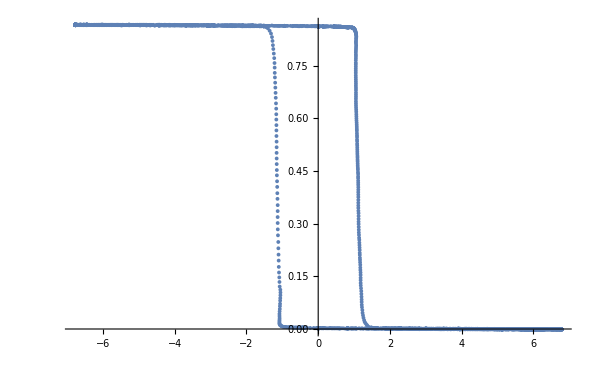

```mathematica
ListPlot[data[[All,{2,3}]]]
```

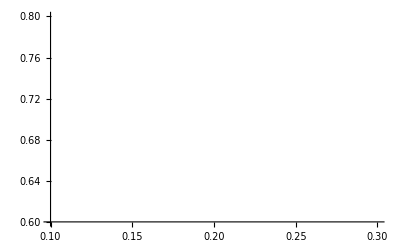

```mathematica
ListPlot[data[[All,{2,3}]],PlotRange->{{0.1,0.3},{0.6,0.8}}]
```